# PeterBurbery/NewLinearAlgebraPaclet

A paclet for linear algebra

## Paclet Manifest

"Documentation"

"English"

"Guides"

"Matrices.nb"DocumentationEnglishGuidesMatrices.nb

"ReferencePages"

"Symbols"

"Antidiagonal.nb"DocumentationEnglishReferencePagesSymbolsAntidiagonal.nb

"DesymmetrizedMatrix.nb"DocumentationEnglishReferencePagesSymbolsDesymmetrizedMatrix.nb

"DeTriangularizableMatrixQ.nb"DocumentationEnglishReferencePagesSymbolsDeTriangularizableMatrixQ.nb

"DeTriangularizeMatrix.nb"DocumentationEnglishReferencePagesSymbolsDeTriangularizeMatrix.nb

"OriginalReferencePages"

"PyramidMatrix.nb"DocumentationEnglishReferencePagesSymbolsPyramidMatrix.nb

"UlamMatrix.nb"DocumentationEnglishReferencePagesSymbolsUlamMatrix.nb

"Tutorials"

"Kernel"

"NewLinearAlgebraPaclet.wl"KernelNewLinearAlgebraPaclet.wl

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

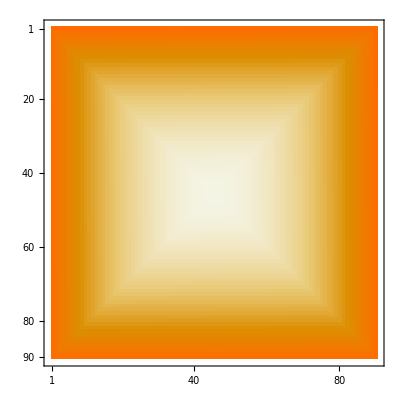

```mathematica
MatrixPlot[ResourceFunction["UlamMatrix"][90]]
```

### Basic Description

This is for linear algebra.

### Details

This paclet loads on startup.

### Primary Context

PeterBurbery`NewLinearAlgebraPaclet`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["PeterBurbery`NewLinearAlgebraPaclet`"];
```

### Basic Examples

Generate an Ulam matrix:

```mathematica
MatrixForm[UlamMatrix[5]]
```

(17 | 16 | 15 | 14 | 13
18 | 5 | 4 | 3 | 12
19 | 6 | 1 | 2 | 11
20 | 7 | 8 | 9 | 10
21 | 22 | 23 | 24 | 25)

Get the antidiagonal of the Ulam matrix:

```mathematica
Antidiagonal[UlamMatrix[5]]
```

{13,3,1,7,21}

Make pyramid matrices:

```mathematica
MatrixForm/@PyramidMatrix/@Range[7]
```

{(1),(1 | 1
1 | 1),(1 | 1 | 1
1 | 2 | 1
1 | 1 | 1),(1 | 1 | 1 | 1
1 | 2 | 2 | 1
1 | 2 | 2 | 1
1 | 1 | 1 | 1),(1 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 1
1 | 2 | 3 | 2 | 1
1 | 2 | 2 | 2 | 1
1 | 1 | 1 | 1 | 1),(1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 2 | 1
1 | 2 | 3 | 3 | 2 | 1
1 | 2 | 3 | 3 | 2 | 1
1 | 2 | 2 | 2 | 2 | 1
1 | 1 | 1 | 1 | 1 | 1),(1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 2 | 2 | 1
1 | 2 | 3 | 3 | 3 | 2 | 1
1 | 2 | 3 | 4 | 3 | 2 | 1
1 | 2 | 3 | 3 | 3 | 2 | 1
1 | 2 | 2 | 2 | 2 | 2 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1)}

Detriangularize a lower-triangularized pyramid matrix:

To get a lower-triangularized or upper-triangularized matrix, use the functions LowerTriangularize and UpperTriangularize, respectively. The matrix that you triangularize should be symmetric:

```mathematica
MatrixForm[pyramidMatrix=PyramidMatrix[7]]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 2 | 2 | 1
1 | 2 | 3 | 3 | 3 | 2 | 1
1 | 2 | 3 | 4 | 3 | 2 | 1
1 | 2 | 3 | 3 | 3 | 2 | 1
1 | 2 | 2 | 2 | 2 | 2 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
SymmetricMatrixQ[pyramidMatrix]
```

True

```mathematica
MatrixForm[lowerTriangularMatrix=LowerTriangularize[pyramidMatrix]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 0 | 0 | 0 | 0 | 0
1 | 2 | 3 | 0 | 0 | 0 | 0
1 | 2 | 3 | 4 | 0 | 0 | 0
1 | 2 | 3 | 3 | 3 | 0 | 0
1 | 2 | 2 | 2 | 2 | 2 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
MatrixForm[DeTriangularizeMatrix[LowerTriangularize[pyramidMatrix]]]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 2 | 2 | 1
1 | 2 | 3 | 3 | 3 | 2 | 1
1 | 2 | 3 | 4 | 3 | 2 | 1
1 | 2 | 3 | 3 | 3 | 2 | 1
1 | 2 | 2 | 2 | 2 | 2 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1)

We have recovered the original matrix:

```mathematica
pyramidMatrix===DeTriangularizeMatrix[LowerTriangularize[pyramidMatrix]]
```

True

### Scope

Give more examples showing the range of features in the paclet:

```mathematica
MyPlot[MyFunction[a,3,4],{a,1,10}]
```

-Graphics-

Use screenshots to show features like notebook styles, palettes and external operations:

```mathematica
ViewWebsite["wolframcloud"]
```

-Graphics-

## Source & Additional Information

### Creator

Peter Burbery

### Source Control Repository

https://github.com/PeterCullenBurbery/linear-algebra-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

linear algebra

matrices

diagonal

antidiagonal

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Antidiagonal

UlamMatrix

### Original Source References and Attributions

Ulam Matrix

Antidiagonal

### Links

Ulam Matrix

Antidiagonal

### Compatibility

#### Wolfram Language Version

13.3+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

This paclet loads on startup. Loading->Startup is in PacletInfo.wl.

## Author Notes

Additional information about limitations, issues, etc.